((-R1 R3 R4+R2 R3 RT+R2 R4 RT) Vcc)/(R2 R3 (R1+RT))

Re[R0]>0&&Im[R0]==0&&R1>0&&R2>0&&R3>(R2 Re[R0])/R1&&R4==-(R0 R2 R3)/(R0 R2-R1 R3)

2082.26

0.

4.44246

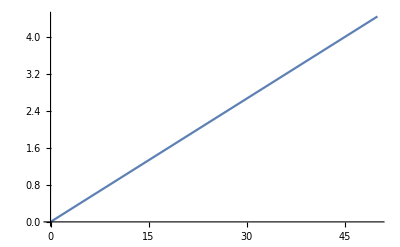

0.+4186.5/(47100.+0.385 T)-(1611.8 T)/(47100.+0.385 T)^2

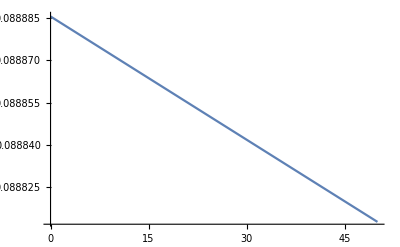

(25 (100.+0.385 T))/(47100.+0.385 T)^2

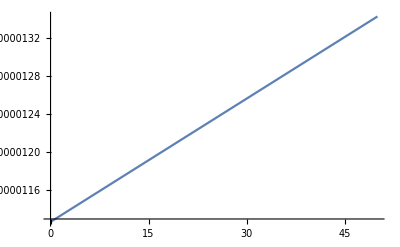

1.34277×10^-6

```mathematica
model=LinearModelFit[{{0, 100},{100, 100+38.5}},{1, T}, T];

system=Vo/.Solve[{
V1==RT/(R1+RT)*Vcc,
V1/R3+(V1-Vcc)/R2==(Vo-V1)/R4
} ,{Vo, V1}][[1]]
MeasurementSystem[Vcc_,R1_, R2_, R3_, R4_, RT_]:=((-R1 R3 R4+R2 R3 RT+R2 R4 RT) Vcc)/(R2 R3 (R1+RT));
Reduce[{MeasurementSystem[5,R1, R2, R3, R4, R0]==0, R1>0, R2>0, R3>0, R4>0}, {R1, R2, R3, R4}]


roffset=-(R0 R2 R3)/(R0 R2-R1 R3)/.{R1->47000, R2->810000,R3->10000,R0->100} //N

Unset[system];
system[T_]=MeasurementSystem[5,47000, 810000, 10000,roffset, model[T]]*1800;
system[0]
system[50]

Plot[system[T], {T, 0, 50}]

sensibility=D[system[T], T]//Expand
Plot[sensibility, {T, 0, 50}]

power[Vcc_,R1_,RT_]=Power[RT/(R1+RT)*Vcc, 2]/RT;
power[5,47000, model[T]]
Plot[power[5,47000, model[T]], {T, 0, 50}]

power[5,47000, model[50]]
```

```mathematica
(C/.Solve[2==1/(2 Pi R C)/.R->100000, C])*10^9//N
```

{795.775}

```mathematica
InverseFunction[model][109]
```

23.3766

```mathematica
system[InverseFunction[model][100+1]]
```

0.

```mathematica
Solve[0.1==30000/c, c]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c→300000.}}

```mathematica
30000/22000//N
```

1.36364

```mathematica
Solve[1/(2 Pi R 0.000001)==2,R]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{R→79577.5}}

```mathematica
1/(2 Pi 68000 0.000001)
```

2.34051

```mathematica
Solve[1*10^-12 R==0.001/1000, R]
```

{{R→1.×10^6}}